### The Integrand in 3 Dimensions:

```mathematica
x[k_,l_]:=k*l
```

```mathematica
Subscript[R, x_][θ_]:=((1.334 * E^(-x/Cos[θ])*Cos[θ])/(1-1.334^2*(Sin[θ])^2)^(1/2))
```

```mathematica
f[z_]:=NIntegrate[2*Pi*Sin[θ]*Subscript[R, z][θ],{θ,0,ArcSin[1/1.334]}]/(2*Pi)
```

```mathematica
Subscript[f, 0]=f[0]
```

0.749625

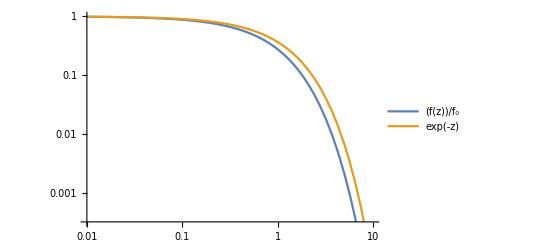

```mathematica
LogLogPlot[{f[z]/Subscript[f, 0],Exp[-z]},{z,0.01,10},PlotLegends->"Expressions"]
```

Difference in normalized case:

```mathematica
dev[z_]:=(f[z]/Subscript[f, 0])/Exp[-z]
```

```mathematica
dev[2.3]
```

0.542567

```mathematica
dev[4.6]
```

0.337781

Difference when not normalized :

```mathematica
dev[z_]:=(f[z])/Exp[-z]
```

```mathematica
dev[2.3]
```

0.406722

```mathematica
dev[4.6]
```

0.253209